```mathematica
X={T,R,θ,ϕ};
```

```mathematica
g={{-1,0,0,0},{0,1,0,0},{0,0,R^2,0},{0,0,0,R^2 Sin[θ]^2}};g//MatrixForm
```

(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | R^2 | 0
0 | 0 | 0 | R^2 Sin[θ]^2)

```mathematica
ginv=g//Inverse//Simplify;ginv//MatrixForm
```

(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1/R^2 | 0
0 | 0 | 0 | Csc[θ]^2/R^2)

(Γ^γ)_αβ = 1/2 g^γζ(g_(αζ,β)+g_(ζβ,α)-g_(αβ,ζ))

```mathematica
Christoffelsudd = Table[1/2 Sum[ginv[[γ,ζ]](D[g[[ζ,β]], X[[α]]]+D[g[[α,ζ]], X[[β]]]-D[g[[α,β]], X[[ζ]]]),{ζ,4}],{γ,4},{α,4},{β,4}]//Simplify;
```

```mathematica
Table[Table[Christoffelsudd[[γ,α,β]],{γ,4}],{α,4},{β,4}]//MatrixForm
```

((0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
1/R
0) | (0
0
0
1/R)
(0
0
0
0) | (0
0
1/R
0) | (0
-R
0
0) | (0
0
0
Cot[θ])
(0
0
0
0) | (0
0
0
1/R) | (0
0
0
Cot[θ]) | (0
-R Sin[θ]^2
-Cos[θ] Sin[θ]
0))

```mathematica
ContractedChristoffelsu=Table[Sum[ginv[[a,b]]Christoffelsudd[[c,a,b]],{a,4},{b,4}],{c,4}]//Simplify
```

{0,-2/R,-Cot[θ]/R^2,0}

```mathematica
ContractedChristoffelsd=Table[Sum[g[[a,b]]ContractedChristoffelsu[[b]],{b,4}],{a,4}]//Simplify
```

{0,-2/R,-Cot[θ],0}

```mathematica
Reimuddd=Table[D[Christoffelsudd[[μ,ν,β]], X[[α]]]-D[Christoffelsudd[[μ,α,ν]], X[[β]]]+Sum[Christoffelsudd[[μ,α,ζ]]Christoffelsudd[[ζ,ν,β]],{ζ,4}]-Sum[Christoffelsudd[[μ,β,ζ]]Christoffelsudd[[ζ,α,ν]],{ζ,4}],{μ,4},{ν,4},{α,4},{β,4}]//Simplify;Reimuddd//MatrixForm
```

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
BoxPsi=Sum[ginv[[a,b]]D[ψ[T,R], X[[a]],X[[b]]],{a,4},{b,4}]-Sum[ContractedChristoffelsu[[c]]D[ψ[T,R], X[[c]]],{c,4}]//Simplify
```

(2 ψ^(0,1)[T,R])/R+ψ^(0,2)[T,R]-ψ^(2,0)[T,R]

```mathematica
ScalarWaveEquation=BoxPsi==0
```

(2 ψ^(0,1)[T,R])/R+ψ^(0,2)[T,R]-ψ^(2,0)[T,R]==0

```mathematica
ic={ψ[0,R]==E^(-R^2)/R,Derivative[1,0][ψ][0,R]==0};
DSolveValue[{ScalarWaveEquation,ic},ψ[T,R],{T,R}]
```

DSolveValue[{(2 ψ^(0,1)[T,R])/R+ψ^(0,2)[T,R]-ψ^(2,0)[T,R]==0,{ψ[0,R]==(ⅇ^(-R^2))/R,ψ^(1,0)[0,R]==0}},ψ[T,R],{T,R}]

```mathematica
DynamicalScalarWaveRule=Solve[ScalarWaveEquation,{D[ψ[T,R], T,T]}]//Flatten//FullSimplify
```

{ψ^(2,0)[T,R]→(2 ψ^(0,1)[T,R])/R+ψ^(0,2)[T,R]}

```mathematica
PiPhiDefinition={P=PI[T,R]==D[ψ[T,R], T],Phi=Φ[T,R]==D[ψ[T,R], R]}
```

{PI[T,R]==ψ^(1,0)[T,R],Φ[T,R]==ψ^(0,1)[T,R]}

```mathematica
{PI[T,R]==Derivative[1,0][ψ][T,R],Φ[T,R]==Derivative[0,1][ψ][T,R]}
```

{PI[T,R]==ψ^(1,0)[T,R],Φ[T,R]==ψ^(0,1)[T,R]}

```mathematica
DerPsiRules=Solve[PiPhiDefinition,{D[ψ[T,R], X[[1]]],D[ψ[T,R], X[[2]]]}]//Flatten
```

{ψ^(1,0)[T,R]→PI[T,R],ψ^(0,1)[T,R]→Φ[T,R]}

```mathematica
InverseDerPsiRules=PiPhiDefinition/.Equal->Rule
```

{PI[T,R]→ψ^(1,0)[T,R],Φ[T,R]→ψ^(0,1)[T,R]}

```mathematica
PiPhiDot=D[PiPhiDefinition, X[[1]]]//Simplify
```

{PI^(1,0)[T,R]==ψ^(2,0)[T,R],Φ^(1,0)[T,R]==ψ^(1,1)[T,R]}

```mathematica
PsiDoubleDotRule={Solve[PiPhiDot[[1]],Derivative[2,0][ψ][T,R]],Solve[PiPhiDot[[2]],Derivative[2,0][ψ][T,R]]}//Flatten
```

{ψ^(2,0)[T,R]→PI^(1,0)[T,R]}

```mathematica
PiPhiDash=D[PiPhiDefinition, X[[2]]]//Simplify
```

{PI^(0,1)[T,R]==ψ^(1,1)[T,R],Φ^(0,1)[T,R]==ψ^(0,2)[T,R]}

```mathematica
PsiDoubleDerRules=Solve[PiPhiDash,{Derivative[1,1][ψ][T,R],Derivative[0,2][ψ][T,R]}]//Simplify//Flatten
```

{ψ^(1,1)[T,R]→PI^(0,1)[T,R],ψ^(0,2)[T,R]→Φ^(0,1)[T,R]}

```mathematica
DerPsiRules[[1]]/.Rule->Equal
```

ψ^(1,0)[T,R]==PI[T,R]

```mathematica
PiEvolutionRule=Solve[ScalarWaveEquation/.PsiDoubleDotRule[[1]]/.PsiDoubleDerRules/.DerPsiRules,Derivative[1,0][PI][T,R]]//Simplify//Flatten
```

{PI^(1,0)[T,R]→(2 Φ[T,R])/R+Φ^(0,1)[T,R]}

```mathematica
PhiEvolutionRule={D[Φ[T,R], X[[1]]]->D[PI[T,R], X[[2]]]}//Simplify//Flatten
```

{Φ^(1,0)[T,R]→PI^(0,1)[T,R]}

```mathematica
PiPhiEvolutionRules={DerPsiRules[[1]],PiEvolutionRule,PhiEvolutionRule}//Flatten
```

{ψ^(1,0)[T,R]→PI[T,R],PI^(1,0)[T,R]→(2 Φ[T,R])/R+Φ^(0,1)[T,R],Φ^(1,0)[T,R]→PI^(0,1)[T,R]}

```mathematica
PiPhiEvolutionEquations=PiPhiEvolutionRules/.Rule->Equal
```

{ψ^(1,0)[T,R]==PI[T,R],PI^(1,0)[T,R]==(2 Φ[T,R])/R+Φ^(0,1)[T,R],Φ^(1,0)[T,R]==PI^(0,1)[T,R]}

```mathematica
PsiConstraint=DerPsiRules[[2]]/.Rule->Equal
```

ψ^(0,1)[T,R]==Φ[T,R]

```mathematica
FirstGoodRescaling={ψ->Function[{T,R},Rψ[T,R]/χ[R]],PI->Function[{T,R},RPI[T,R]/χ[R]],Φ->Function[{T,R},(RΦ[T,R]-ψ[T,R]D[χ[R], R])/χ[R]]}
```

{ψ→Function[{T,R},Rψ[T,R]/χ[R]],PI→Function[{T,R},RPI[T,R]/χ[R]],Φ→Function[{T,R},(RΦ[T,R]-ψ[T,R] ∂_R χ[R])/χ[R]]}

```mathematica
FirstGoodRescaledEquations=Solve[(PiPhiEvolutionRules/.FirstGoodRescaling/.DerPsiRules/.Rule->Equal//Simplify)/.FirstGoodRescaling/.PI->Function[{T,R},RPI[T,R]/χ[R]]/.ψ->Function[{T,R},Rψ[T,R]/χ[R]],{Derivative[1,0][Rψ][T,R],Derivative[1,0][RPI][T,R],Derivative[1,0][RΦ][T,R]}]//Flatten//Simplify
```

{Rψ^(1,0)[T,R]→RPI[T,R],RPI^(1,0)[T,R]→(2 RΦ[T,R] χ[R] (χ[R]-R χ'[R])+Rψ[T,R] (2 R χ'[R]^2-χ[R] (2 χ'[R]+R χ''[R]))+R χ[R]^2 RΦ^(0,1)[T,R])/(R χ[R]^2),RΦ^(1,0)[T,R]→RPI^(0,1)[T,R]}

```mathematica
Collect[FirstGoodRescaledEquations,{RΦ[T,R],Rψ[T,R]},Simplify]
```

{Rψ^(1,0)[T,R]→RPI[T,R],RPI^(1,0)[T,R]→RΦ[T,R] (2/R-(2 χ'[R])/χ[R])+(Rψ[T,R] (2 R χ'[R]^2-χ[R] (2 χ'[R]+R χ''[R])))/(R χ[R]^2)+RΦ^(0,1)[T,R],RΦ^(1,0)[T,R]→RPI^(0,1)[T,R]}

```mathematica
coorsubs={T->Tf[t,r],R->Rf[r]}
```

{T→Tf[t,r],R→Rf[r]}

```mathematica
Xcoor={T,R};x={t,r};
```

```mathematica
(*corresponding Jacobian (dX/dx) and its inverse (dx/dX)*)
(Jac=Table[D[Xcoor[[c2]]/.coorsubs,x[[c1]]],{c1,1,Length@x},{c2,1,Length@Xcoor}])//MatrixForm (*{{D[Texpr,t],D[Texpr,r]},{D[Rexpr,t],D[Rexpr,r]}}*)
(*Here, rows vary with c1, or x, and columns with c2, i.e. X.*)
(InvJac=Inverse@Jac)//MatrixForm(*Here, rows vary with X and columns with x.*)
Jac.InvJac//MatrixForm
```

(Tf^(1,0)[t,r] | 0
Tf^(0,1)[t,r] | Rf'[r])

(1/(Tf^(1,0)[t,r]) | 0
-(Tf^(0,1)[t,r])/(Rf'[r] Tf^(1,0)[t,r]) | 1/Rf'[r])

(1 | 0
0 | 1)

```mathematica
derchange={Table[D[zz_[T,R],Xcoor[[count]]]->Sum[InvJac[[count,sum]]D[zz[t,r],x[[sum]]],{sum,1,Length@x}],{count,1,Length@Xcoor}](*,D[zz_[R],Xcoor[[2]]]->InvJac[[2,2]]D[zz[r],x[[2]]]*)}//Flatten
```

{zz_^(1,0)[T,R]→(zz^(1,0)[t,r])/(Tf^(1,0)[t,r]),zz_^(0,1)[T,R]→(zz^(0,1)[t,r])/Rf'[r]-(Tf^(0,1)[t,r] zz^(1,0)[t,r])/(Rf'[r] Tf^(1,0)[t,r])}

```mathematica
changerules={derchange,zz_[T,R]->zz[t,r](*,zz_[R]->zz[Rf[r]]*)}//Flatten
```

{zz_^(1,0)[T,R]→(zz^(1,0)[t,r])/(Tf^(1,0)[t,r]),zz_^(0,1)[T,R]→(zz^(0,1)[t,r])/Rf'[r]-(Tf^(0,1)[t,r] zz^(1,0)[t,r])/(Rf'[r] Tf^(1,0)[t,r]),zz_[T,R]→zz[t,r]}

T = t + H(R) = t + R(r) - r;
Taking dH/dR = (R’ - 1)/R’
=> H’ = dH/dr = H’ R’ = R’ (R’ - 1)/R’  = R’ - 1
=> H(r) = R(r) - r, demanding that H(0) = 0.

```mathematica
TRule=Tf->Function[{t,r},t+Rf[r]-r]
```

Tf→Function[{t,r},t+Rf[r]-r]

```mathematica
changerules/.TRule
```

{zz_^(1,0)[T,R]→zz^(1,0)[t,r],zz_^(0,1)[T,R]→(zz^(0,1)[t,r])/Rf'[r]-((-1+Rf'[r]) zz^(1,0)[t,r])/Rf'[r],zz_[T,R]→zz[t,r]}

```mathematica
GoodRescaledHypGridFunctions=FirstGoodRescaling/.changerules//Flatten
```

{ψ→Function[{t,r},Rψ[t,r]/χ[R]],PI→Function[{t,r},RPI[t,r]/χ[R]],Φ→Function[{t,r},(RΦ[t,r]-ψ[t,r] ∂_R χ[R])/χ[R]]}

```mathematica
FirstGoodRescalingHypSlices=FirstGoodRescaling/.changerules/.TRule/.coorsubs
```

{ψ→Function[{t,r},Rψ[t,r]/χ[Rf[r]]],PI→Function[{t,r},RPI[t,r]/χ[Rf[r]]],Φ→Function[{t,r},(RΦ[t,r]-ψ[t,r] ∂_Rf[r] χ[Rf[r]])/χ[Rf[r]]]}

```mathematica
χRule={χ-> Function[{Rf},Sqrt[1+Rf^2]]}
```

{χ→Function[{Rf},√(1+Rf^2)]}

```mathematica
GoodRescaledEquationsHypSlices=Solve[FirstGoodRescaledEquations/.changerules/.TRule/.coorsubs/.Rule->Equal//Simplify,{Derivative[1,0][Rψ][t,r], Derivative[1,0][RPI][t,r],Derivative[1,0][RΦ][t,r]}]//Flatten//FullSimplify//Expand
```

{Rψ^(1,0)[t,r]→RPI[t,r],RPI^(1,0)[t,r]→(2 RΦ[t,r] Rf'[r]^2)/(Rf[r] (-1+2 Rf'[r]))-(2 RΦ[t,r] Rf'[r]^2 χ'[Rf[r]])/(χ[Rf[r]] (-1+2 Rf'[r]))-(2 Rψ[t,r] Rf'[r]^2 χ'[Rf[r]])/(Rf[r] χ[Rf[r]] (-1+2 Rf'[r]))+(2 Rψ[t,r] Rf'[r]^2 χ'[Rf[r]]^2)/(χ[Rf[r]]^2 (-1+2 Rf'[r]))-(Rψ[t,r] Rf'[r]^2 χ''[Rf[r]])/(χ[Rf[r]] (-1+2 Rf'[r]))+(RPI^(0,1)[t,r])/(-1+2 Rf'[r])-(Rf'[r] RPI^(0,1)[t,r])/(-1+2 Rf'[r])+(Rf'[r] RΦ^(0,1)[t,r])/(-1+2 Rf'[r]),RΦ^(1,0)[t,r]→(2 RΦ[t,r] Rf'[r])/(Rf[r] (-1+2 Rf'[r]))-(2 RΦ[t,r] Rf'[r]^2)/(Rf[r] (-1+2 Rf'[r]))-(2 RΦ[t,r] Rf'[r] χ'[Rf[r]])/(χ[Rf[r]] (-1+2 Rf'[r]))-(2 Rψ[t,r] Rf'[r] χ'[Rf[r]])/(Rf[r] χ[Rf[r]] (-1+2 Rf'[r]))+(2 RΦ[t,r] Rf'[r]^2 χ'[Rf[r]])/(χ[Rf[r]] (-1+2 Rf'[r]))+(2 Rψ[t,r] Rf'[r]^2 χ'[Rf[r]])/(Rf[r] χ[Rf[r]] (-1+2 Rf'[r]))+(2 Rψ[t,r] Rf'[r] χ'[Rf[r]]^2)/(χ[Rf[r]]^2 (-1+2 Rf'[r]))-(2 Rψ[t,r] Rf'[r]^2 χ'[Rf[r]]^2)/(χ[Rf[r]]^2 (-1+2 Rf'[r]))-(Rψ[t,r] Rf'[r] χ''[Rf[r]])/(χ[Rf[r]] (-1+2 Rf'[r]))+(Rψ[t,r] Rf'[r]^2 χ''[Rf[r]])/(χ[Rf[r]] (-1+2 Rf'[r]))+(Rf'[r] RPI^(0,1)[t,r])/(-1+2 Rf'[r])+(RΦ^(0,1)[t,r])/(-1+2 Rf'[r])-(Rf'[r] RΦ^(0,1)[t,r])/(-1+2 Rf'[r])}

```mathematica
ScriLimitRule={ψ[t,r]->1/Rf[r],D[χ[Rf[r]], Rf[r]]->1,χ[Rf[r]]->Rf[r],D[D[χ[Rf[r]], Rf[r]], Rf[r]]->0,RPI[t,r]->Rf[r] 1/2(PiPlus[t,r]+PiMinus[t,r]),RΦ[t,r]->Rf[r] 1/2(PiPlus[t,r]-PiMinus[t,r])+1/Rf[r],Derivative[0,1][ψ][t,r]->1/2(PiPlus[t,r]-PiMinus[t,r]) ,H'[Rf[r]]->1-1/D[Rf[r], r] }
PiPlusMinusRules={PiPlus[t,r]->1/Rf[r]^2,PiMinus[t,r]->1/Rf[r]}
```

{ψ[t,r]→1/Rf[r],χ'[Rf[r]]→1,χ[Rf[r]]→Rf[r],χ''[Rf[r]]→0,RPI[t,r]→1/2 (PiMinus[t,r]+PiPlus[t,r]) Rf[r],RΦ[t,r]→1/Rf[r]+1/2 (-PiMinus[t,r]+PiPlus[t,r]) Rf[r],ψ^(0,1)[t,r]→1/2 (-PiMinus[t,r]+PiPlus[t,r]),H'[Rf[r]]→1-1/Rf'[r]}

{PiPlus[t,r]→1/Rf[r]^2,PiMinus[t,r]→1/Rf[r]}

```mathematica
GoodRescaledEquationsHypSlices/.ScriLimitRule/.PiPlusMinusRules//Flatten//FullSimplify//Expand
```

{Rψ^(1,0)[t,r]→1/2+1/(2 Rf[r]),RPI^(1,0)[t,r]→(RPI^(0,1)[t,r])/(-1+2 Rf'[r])-(Rf'[r] RPI^(0,1)[t,r])/(-1+2 Rf'[r])+(Rf'[r] RΦ^(0,1)[t,r])/(-1+2 Rf'[r]),RΦ^(1,0)[t,r]→(Rf'[r] RPI^(0,1)[t,r])/(-1+2 Rf'[r])+(RΦ^(0,1)[t,r])/(-1+2 Rf'[r])-(Rf'[r] RΦ^(0,1)[t,r])/(-1+2 Rf'[r])}

```mathematica
Collect[GoodRescaledEquationsHypSlices,{RΦ[t,r],Rψ[t,r],RPI[t,r],Derivative[0,1][RPI][t,r], Derivative[0,1][RΦ][t,r]},Simplify]/.χ->Function[x,x]
```

{Rψ^(1,0)[t,r]→RPI[t,r],RPI^(1,0)[t,r]→((1-Rf'[r]) RPI^(0,1)[t,r])/(-1+2 Rf'[r])+(Rf'[r] RΦ^(0,1)[t,r])/(-1+2 Rf'[r]),RΦ^(1,0)[t,r]→(Rf'[r] RPI^(0,1)[t,r])/(-1+2 Rf'[r])+((1-Rf'[r]) RΦ^(0,1)[t,r])/(-1+2 Rf'[r])}

```mathematica
Collect[GoodRescaledEquationsHypSlices/.χ->Function[Rf,Sqrt[1+Rf^2]]/.Rf->Function[r,r/(1-r^2/s^2)],{RΦ[t,r],Rψ[t,r],RPI[t,r],Derivative[0,1][RPI][t,r], Derivative[0,1][RΦ][t,r]},FullSimplify]
```

{Rψ^(1,0)[t,r]→RPI[t,r],RPI^(1,0)[t,r]→(2 (r-s) s^2 (r+s) (r^2+s^2)^2 RΦ[t,r])/(r (r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))+(3 s^4 (r^4-s^4)^2 Rψ[t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2))^2)+((r^4-3 r^2 s^2) RPI^(0,1)[t,r])/(-r^4+4 r^2 s^2+s^4)+(s^2 (r^2+s^2) RΦ^(0,1)[t,r])/(-r^4+4 r^2 s^2+s^4),RΦ^(1,0)[t,r]→(2 r (r-s) (r+s) (r^2-3 s^2) (r^2+s^2) RΦ[t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))+(3 (r^2-3 s^2) (r^2+s^2) (r^3 s-r s^3)^2 Rψ[t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2))^2)+(s^2 (r^2+s^2) RPI^(0,1)[t,r])/(-r^4+4 r^2 s^2+s^4)+((r^4-3 r^2 s^2) RΦ^(0,1)[t,r])/(-r^4+4 r^2 s^2+s^4)}

```mathematica
Collect[GoodRescaledEquationsHypSlices[[2]]/.χ->Function[x,Sqrt[1+x^2]]/.Rf->Function[r,r/(1-r^2/s^2)],{RΦ[t,r],Rψ[t,r],RPI[t,r],Derivative[0,1][RPI][t,r], Derivative[0,1][RΦ][t,r]},FullSimplify]
```

RPI^(1,0)[t,r]→(2 (r-s) s^2 (r+s) (r^2+s^2)^2 RΦ[t,r])/(r (r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))+(3 s^4 (r^4-s^4)^2 Rψ[t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2))^2)+((r^4-3 r^2 s^2) RPI^(0,1)[t,r])/(-r^4+4 r^2 s^2+s^4)+(s^2 (r^2+s^2) RΦ^(0,1)[t,r])/(-r^4+4 r^2 s^2+s^4)

```mathematica
(2 (r-s) s^2 (r+s) (r^2+s^2)^2 RΦ[t,r])/(r (r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))//Expand
```

(2 r^5 s^2 RΦ[t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))+(2 r^3 s^4 RΦ[t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))-(2 r s^6 RΦ[t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))-(2 s^8 RΦ[t,r])/(r (r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))

```mathematica
(2 r^5 s^2 RΦ[t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))+(2 r^3 s^4 RΦ[t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))-(2 r s^6 RΦ[t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))//FullSimplify
```

(2 r s^2 (r^4+r^2 s^2-s^4) RΦ[t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))

```mathematica
Step1 = Collect[GoodRescaledEquationsHypSlices[[2]]/.χ->Function[x,Sqrt[1+x^2]]/.Rf->Function[r,r/(1-r^2/s^2)],{RΦ[t,r],Rψ[t,r],RPI[t,r],Derivative[0,1][RPI][t,r], Derivative[0,1][RΦ][t,r]},FullSimplify]/.(2 (r-s) s^2 (r+s) (r^2+s^2)^2 RΦ[t,r])/(r (r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))->-(2 s^8 RΦ[t,r])/(r (r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))+(2 r s^2 (r^4+r^2 s^2-s^4) RΦ[t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))
```

RPI^(1,0)[t,r]→-(2 s^8 RΦ[t,r])/(r (r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))+(2 r s^2 (r^4+r^2 s^2-s^4) RΦ[t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))+(3 s^4 (r^4-s^4)^2 Rψ[t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2))^2)+((r^4-3 r^2 s^2) RPI^(0,1)[t,r])/(-r^4+4 r^2 s^2+s^4)+(s^2 (r^2+s^2) RΦ^(0,1)[t,r])/(-r^4+4 r^2 s^2+s^4)

```mathematica
(s^2 (r^2+s^2) Derivative[0,1][RΦ][t,r])/(-r^4+4 r^2 s^2+s^4)+(s^8 Derivative[0,1][RΦ][t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))//FullSimplify
```

-(r^2 s^2 (r^4-s^4+s^6+r^2 s^2 (-1+s^2)) RΦ^(0,1)[t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))

```mathematica
Collect[-(2 s^8 RΦ[t,r])/(r (r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))-(s^8 Derivative[0,1][RΦ][t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2))),s^8/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))]
```

(s^8 (-(2 RΦ[t,r])/r-RΦ^(0,1)[t,r]))/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))

```mathematica
FinalEqRPi =Step1/.-(2 s^8 RΦ[t,r])/(r (r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))+(s^2 (r^2+s^2) Derivative[0,1][RΦ][t,r])/(-r^4+4 r^2 s^2+s^4)->-(r^2 s^2 (r^4-s^4+s^6+r^2 s^2 (-1+s^2)) Derivative[0,1][RΦ][t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))-(s^8 (+(2 RΦ[t,r])/r+Derivative[0,1][RΦ][t,r]))/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))
```

RPI^(1,0)[t,r]→(2 r s^2 (r^4+r^2 s^2-s^4) RΦ[t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))+(3 s^4 (r^4-s^4)^2 Rψ[t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2))^2)+((r^4-3 r^2 s^2) RPI^(0,1)[t,r])/(-r^4+4 r^2 s^2+s^4)-(r^2 s^2 (r^4-s^4+s^6+r^2 s^2 (-1+s^2)) RΦ^(0,1)[t,r])/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))-(s^8 ((2 RΦ[t,r])/r+RΦ^(0,1)[t,r]))/((r^4-4 r^2 s^2-s^4) (r^4+s^4+r^2 s^2 (-2+s^2)))

```mathematica
FinalEqRPi/.(r^4+s^4+r^2 s^2 (-2+s^2))->A/.(r^4-4 r^2 s^2-s^4)->B/.(r-s)->C/.(-r+s) ->-C/.(r^4-3 r^2 s^2)->D/.(r^2+s^2)->F/.(r^2-3 s^2)->G/.-r^4+4 r^2 s^2+s^4->H/.(r^3 s-r s^3)->L/.(r^4+r^2 s^2-s^4)->M/.(r^4-s^4+s^6+r^2 s^2 (-1+s^2)) ->N/.r^4-s^4->O
```

RPI^(1,0)[t,r]→(2 M r s^2 RΦ[t,r])/(A B)+(3 O^2 s^4 Rψ[t,r])/(A^2 B)+(D RPI^(0,1)[t,r])/H-(N r^2 s^2 RΦ^(0,1)[t,r])/(A B)-(s^8 ((2 RΦ[t,r])/r+RΦ^(0,1)[t,r]))/(A B)

```mathematica
Collect[GoodRescaledEquationsHypSlices[[3]]/.χ->Function[x,Sqrt[1+x^2]]/.Rf->Function[r,r/(1-r^2/s^2)],{RΦ[t,r],Rψ[t,r],RPI[t,r],Derivative[0,1][RPI][t,r], Derivative[0,1][RΦ][t,r]},FullSimplify]/.(r^4+s^4+r^2 s^2 (-2+s^2))->A/.(r^4-4 r^2 s^2-s^4)->B/.(r-s)->C/.(-r+s) ->-C/.(r^4-3 r^2 s^2)->D/.(r^2+s^2)->F/.(r^2-3 s^2)->G/.-r^4+4 r^2 s^2+s^4->H/.(r^3 s-r s^3)->L/.(r^4+r^2 s^2-s^4)->M/.(r^4-s^4+s^6+r^2 s^2 (-1+s^2)) ->N/.r^4-s^4->O
```

RΦ^(1,0)[t,r]→(2 C F G r (r+s) RΦ[t,r])/(A B)+(3 F G L^2 Rψ[t,r])/(A^2 B)+(F s^2 RPI^(0,1)[t,r])/H+(D RΦ^(0,1)[t,r])/H

## Variables transformation and rescaling of the solutions

Setting initial data

Scalar field:

```mathematica
F=Function[{x},A*E^(-(ds*x)^2)]
```

Function[{x},A ⅇ^(-(ds x)^2)]

Derivative of the scalar field

```mathematica
DF=D[F[Rf[r]],Rf[r]]
```

-2 A ds^2 ⅇ^(-ds^2 Rf[r]^2) Rf[r]

```mathematica
Solution =Function[{x,z},((x+z)F[x+z]+(-x+z)F[-x+z])/(2z)]
```

Function[{x,z},((x+z) F[x+z]+(-x+z) F[-x+z])/(2 z)]

```mathematica
Solution[Tf[t,r],Rf[r]]*χ[Rf[r]]//FullSimplify
```

((A ⅇ^(-ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]-Tf[t,r])+A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]+Tf[t,r])) χ[Rf[r]])/(2 Rf[r])

Rescaling

```mathematica
F[Rf[r]]*χ[Rf[r]]/.TRule
```

A ⅇ^(-ds^2 Rf[r]^2) χ[Rf[r]]

```mathematica
D[F[Rf[r]]*χ[Rf[r]],Rf[r]]
```

-2 A ds^2 ⅇ^(-ds^2 Rf[r]^2) Rf[r] χ[Rf[r]]+A ⅇ^(-ds^2 Rf[r]^2) χ'[Rf[r]]

```mathematica
Solution[Tf[t,r],Rf[r]]*χ[Rf[r]]/.TRule/.Rf->Function[r,r/(1-r^2/s^2)]/.χ->Function[x,Sqrt[1+x^2]]
```

(√(1+r^2/((1-r^2/s^2)^2)) (1-r^2/s^2) (A ⅇ^(-ds^2 (r-t)^2) (r-t)+A ⅇ^(-ds^2 (-r+(2 r)/(1-r^2/s^2)+t)^2) (-r+(2 r)/(1-r^2/s^2)+t)))/(2 r)

```mathematica
Solution[Tf[t,r],Rf[r]]*χ[Rf[r]]/.TRule/.t->0
```

((A ⅇ^(-ds^2 r^2) r+A ⅇ^(-ds^2 (-r+2 Rf[r])^2) (-r+2 Rf[r])) χ[Rf[r]])/(2 Rf[r])

```mathematica
SolutionPrime = D[Solution[Tf[t,r],Rf[r]],Rf[r]]
```

-(A ⅇ^(-ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]-Tf[t,r])+A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]+Tf[t,r]))/(2 Rf[r]^2)+1/(2 Rf[r])(A ⅇ^(-ds^2 (Rf[r]-Tf[t,r])^2)+A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2)-2 A ds^2 ⅇ^(-ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]-Tf[t,r])^2-2 A ds^2 ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]+Tf[t,r])^2)

```mathematica
RSolutionPrime = SolutionPrime*χ[Rf[r]]+Solution[Tf[t,r],Rf[r]]*D[χ[Rf[r]], Rf[r]]/.TRule//FullSimplify
```

1/(2 Rf[r]^2)(A (ⅇ^(-ds^2 (r-t)^2) (-r+t+(1-2 ds^2 (r-t)^2) Rf[r])+ⅇ^(-ds^2 (-r+t+2 Rf[r])^2) (r-t-Rf[r] (1+2 ds^2 (r-t)^2+8 ds^2 Rf[r] (-r+t+Rf[r])))) χ[Rf[r]]+Rf[r] (A ⅇ^(-ds^2 (r-t)^2) (r-t)+A ⅇ^(-ds^2 (-r+t+2 Rf[r])^2) (-r+t+2 Rf[r])) χ'[Rf[r]])

Computing the initial data for the scalar field

```mathematica
Solution[Tf[t,r],Rf[r]]*χ[Rf[r]]/.TRule/.Rf->Function[r,r/(1-r^2/s^2)]/.χ->Function[x,Sqrt[1+x^2]]/.t->0//FullSimplify
```

1/2 A √(1+r^2/((-1+r^2/s^2)^2)) (1-r^2/s^2) (ⅇ^(-ds^2 r^2)-(ⅇ^(-(ds^2 r^2 (r^2+s^2)^2)/((r^2-s^2)^2)) (r^2+s^2))/(r^2-s^2))

Since some term diverges, we have to compute the limit for r->s

```mathematica
1/2 A √(1+r^2/((-1+r^2/s^2)^2)) (1-r^2/s^2) ⅇ^(-ds^2 r^2)/.A->1/.√(1+r^2/((-1+r^2/s^2)^2)) (1-r^2/s^2)->√((-1+r^2/s^2)^2+r^2)
```

1/2 ⅇ^(-ds^2 r^2) √(r^2+(-1+r^2/s^2)^2)

```mathematica
1/2 ⅇ^(-ds^2 r^2) √(r^2+(-1+r^2/s^2)^2)/.r->s/.s->5/.ds->1/5
```

5/(2 ⅇ)

Computing the initial data for the space derivative of the scalar field

```mathematica
InitialRSolutionPrime = RSolutionPrime/.TRule/.t->0//FullSimplify
```

1/(2 Rf[r]^2)(A (ⅇ^(-ds^2 r^2) (-r+Rf[r]-2 ds^2 r^2 Rf[r])+ⅇ^(-ds^2 (r-2 Rf[r])^2) (r-Rf[r] (1+2 ds^2 r^2+8 ds^2 Rf[r] (-r+Rf[r])))) χ[Rf[r]]+(A ⅇ^(-ds^2 r^2) r-A ⅇ^(-ds^2 (r-2 Rf[r])^2) (r-2 Rf[r])) Rf[r] χ'[Rf[r]])

```mathematica
InitialRSolutionPrime/.ⅇ^(-ds^2 (r-2 Rf[r])^2)->B/.(r-2 Rf[r])->C/.-r+Rf[r]->D/.ds^2 r^2->G
```

(A (ⅇ^-G (D-2 G Rf[r])+B (r-Rf[r] (1+2 G+8 D ds^2 Rf[r]))) χ[Rf[r]]+(-A B C+A ⅇ^-G r) Rf[r] χ'[Rf[r]])/(2 Rf[r]^2)

```mathematica
1/(2 Rf[r]^2)A ⅇ^(-ds^2 r^2) (Rf[r]-2 ds^2 r^2 Rf[r])*χ[Rf[r]]/.χ->Function[x,Sqrt[1+x^2]]
```

(A ⅇ^(-ds^2 r^2) (Rf[r]-2 ds^2 r^2 Rf[r]) √(1+Rf[r]^2))/(2 Rf[r]^2)

```mathematica
(A ⅇ^(-ds^2 r^2) (Rf[r]-2 ds^2 r^2 Rf[r])Rf[r])/(2 Rf[r]^2)//FullSimplify
```

1/2 ⅇ^(-ds^2 r^2) (A-2 A ds^2 r^2)

```mathematica
1/2 ⅇ^(-ds^2 r^2) (A-2 A ds^2 r^2)/.r->s
```

1/2 ⅇ^(-ds^2 s^2) (A-2 A ds^2 s^2)

```mathematica
PerPlot=RSolutionPrime/.TRule/.t->0/.Rf->Function[r,r/(1-r^2/s^2)]/.χ->Function[x,Sqrt[1+x^2]]/.A->1/.ds->1/5/.s->5
```

((1-r^2/25)^2 ((r^2 (ⅇ^(-r^2/25) r+ⅇ^(-1/25 (-r+(2 r)/(1-r^2/25))^2) (-r+(2 r)/(1-r^2/25))))/((1-r^2/25)^2 √(1+r^2/((1-r^2/25)^2)))+√(1+r^2/((1-r^2/25)^2)) (ⅇ^(-r^2/25) (-r+(r (1-(2 r^2)/25))/(1-r^2/25))+ⅇ^(-1/25 (-r+(2 r)/(1-r^2/25))^2) (r-(r (1+(2 r^2)/25+(8 r (-r+r/(1-r^2/25)))/(25 (1-r^2/25))))/(1-r^2/25)))))/(2 r^2)

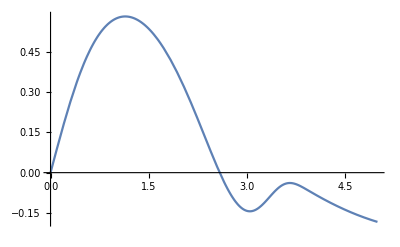

```mathematica
Plot[PerPlot,{r,0,5}]
```

Computing the intial data for the time derivative of the scalar field

```mathematica
RSolutionDot= D[Solution[Tf[t,r],Rf[r]]*χ[Rf[r]],Tf[t,r]]
```

1/(2 Rf[r])(-A ⅇ^(-ds^2 (Rf[r]-Tf[t,r])^2)+A ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2)+2 A ds^2 ⅇ^(-ds^2 (Rf[r]-Tf[t,r])^2) (Rf[r]-Tf[t,r])^2-2 A ds^2 ⅇ^(-ds^2 (Rf[r]+Tf[t,r])^2) (Rf[r]+Tf[t,r])^2) χ[Rf[r]]

```mathematica
RSolutionDot/.TRule/.t->0/.-ds^2 (-r+2 Rf[r])^2->B/.ds^2 r^2->C/.-ds^2 r^2->-C/.(-r+2 Rf[r])^2->D
```

((A ⅇ^B-2 A D ds^2 ⅇ^B-A ⅇ^-C+2 A C ⅇ^-C) χ[Rf[r]])/(2 Rf[r])

We compute the initial value for r=s

```mathematica
RSolutionDot/.TRule/.t->0
```

((-A ⅇ^(-ds^2 r^2)+A ⅇ^(-ds^2 (-r+2 Rf[r])^2)+2 A ds^2 ⅇ^(-ds^2 r^2) r^2-2 A ds^2 ⅇ^(-ds^2 (-r+2 Rf[r])^2) (-r+2 Rf[r])^2) χ[Rf[r]])/(2 Rf[r])

```mathematica
(-A ⅇ^(-ds^2 r^2)+2 A ds^2 ⅇ^(-ds^2 r^2) r^2)/2/.-ds^2 (-r+2 Rf[r])^2->B/.ds^2 r^2->C/.-ds^2 r^2->-C/.(-r+2 Rf[r])^2->D
```

1/2 (-A ⅇ^-C+2 A C ⅇ^-C)

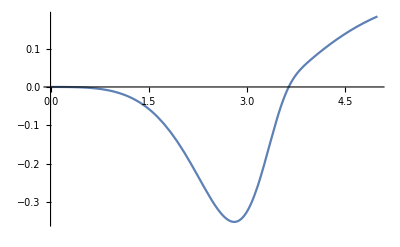

```mathematica
Plot[RSolutionDot/.TRule/.t->0/.Rf->Function[r,r/(1-r^2/s^2)]/.χ->Function[x,Sqrt[1+x^2]]/.A->1/.ds->1/5/.s->5,{r,0,5}]
```